```mathematica
ee2mumu =Import["/Users/hevanderdacosta/Desktop/Pythia-Output-Data-Files/ee_mumu_cosine_Distribution.dat", "Table"]
```

{{5,-4.16545,-0.46915,-2.72356,-0.544833},{5,0.210762,3.3598,3.69542,0.73925},{5,-2.02128,1.14959,4.42512,0.885222},{5,2.5978,0.915039,-4.17169,-0.834524},15032,{5,1.15911,4.84957,0.356376,0.0712911},{5,-1.99746,4.57668,-0.230136,-0.0460375},{5,4.53489,-1.90558,0.890176,0.178075}}
 |  |  |  |

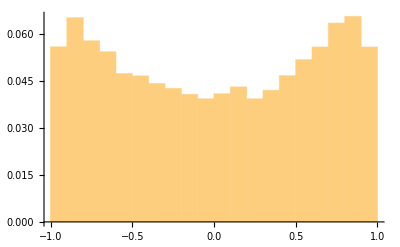

```mathematica
p1 =Histogram[ee2mumu[[All, 5]],Automatic, "Probability"]
```

```mathematica
σ[cθ_] :=Module[{α, m, nrg, d},
{α=1/137, m=.1057, nrg = 10, d = 5} ;2π* (α^2/(4*nrg^2))*(Sqrt[(1-(m^2/d^2))])*((1+(m^2/d^2))+(1-(m^2/d^2))*((cθ)^2))]
```

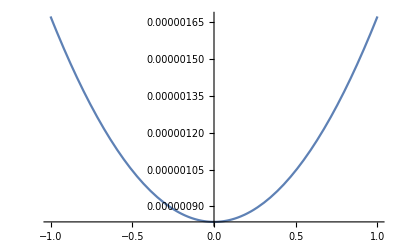

```mathematica
Plot[σ[cθ],{cθ, -1, 1}]
```

```mathematica
σtotal:= Module[{α, m, nrg, d}, {α=1/137, m = .1057, nrg = 10, d = 5};((4*π*(α^2)/(3*nrg^2))*(Sqrt[1-m^2/d^2])*(1+(0.5*m^2/d^2)))]
```

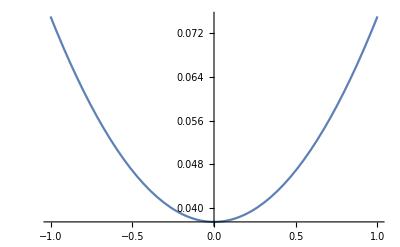

```mathematica
p2=Plot[0.1*σ[cθ]/σtotal, {cθ, -1, 1}]
```

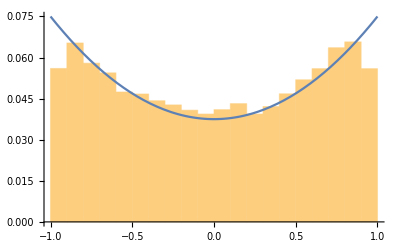

```mathematica
Show[p1,p2]
```